```mathematica
"MANUEL DE LA CRUZ GONZÁLEZ 70909708H"
"EJERCICIO 1"
```

```mathematica
f=DSolve[{y'[x]==y[x]-ⅇ^x*Cos[x]*Sin[x],y[0]==0},y,x][[1,1,2]]
```

Function[{x},1/2 ⅇ^x (-1+Cos[x]^2)]

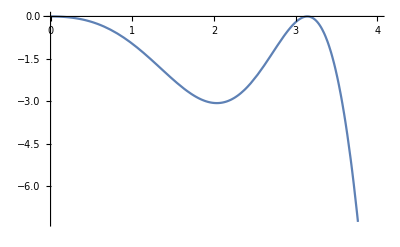

```mathematica
grafanalitica=Plot[f[x],{x,0,4}]
```

```mathematica
taylorprimer=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Taylorprimer.txt","Table"]


Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Heun.txt","Table"]
Eulermod=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Eulermodificado.txt","Table"]
RK4=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Rugekutta4.txt","Table"]
```

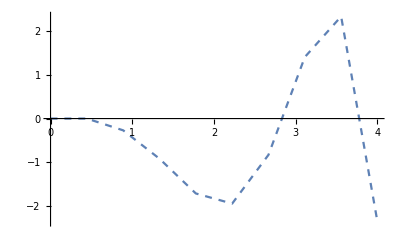

```mathematica
g1=ListLinePlot[taylorprimer,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

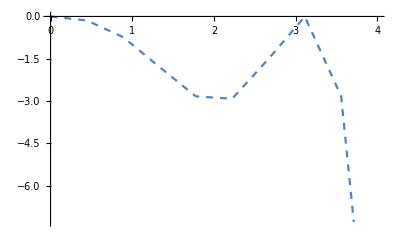

```mathematica
g2=ListLinePlot[Heun,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

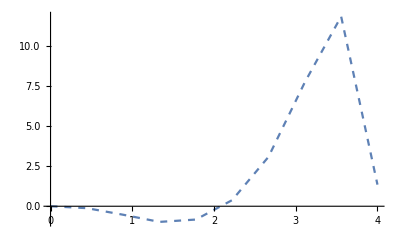

```mathematica
g3=ListLinePlot[Eulermod,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

```mathematica
g4=ListLinePlot[RK4,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

-Graphics-

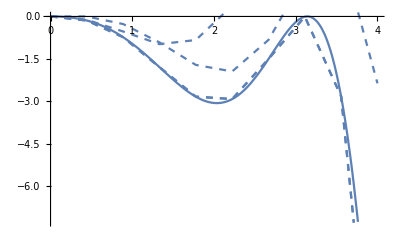

```mathematica
Show[grafanalitica,g1,g2,g3,g4]
```

```mathematica
"AHORA PARA 25 PUNTOS"
```

```mathematica
taylorprimer=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Taylorprimer.txt","Table"]
Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Heun.txt","Table"]
Eulermod=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Eulermodificado.txt","Table"]
RK4=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Rugekutta4.txt","Table"]
```

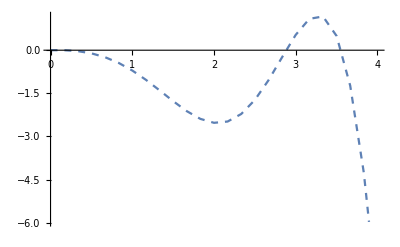

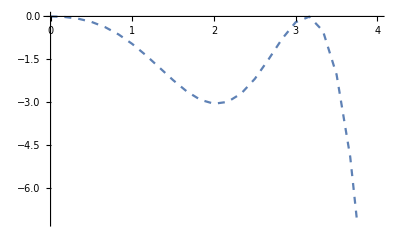

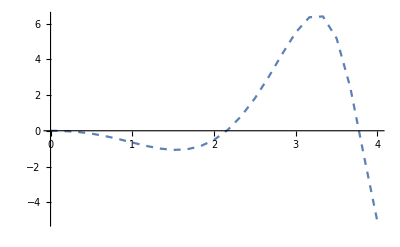

-Graphics-

```mathematica
g1=ListLinePlot[taylorprimer,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g2=ListLinePlot[Heun,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g3=ListLinePlot[Eulermod,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g4=ListLinePlot[RK4,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

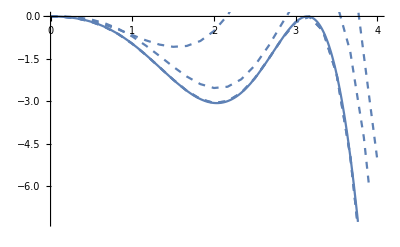

```mathematica
Show[grafanalitica,g1,g2,g3,g4]
```

```mathematica
"AHORA CON 50 PARES"
```

```mathematica
taylorprimer=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Taylorprimer.txt","Table"]
Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Heun.txt","Table"]
Eulermod=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Eulermodificado.txt","Table"]
RK4=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Rugekutta4.txt","Table"]
```

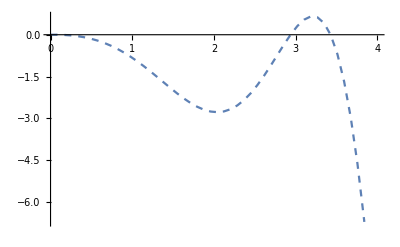

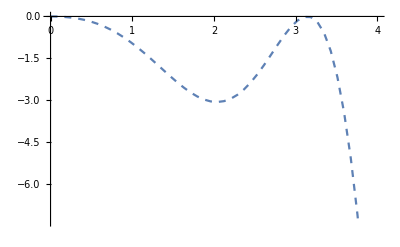

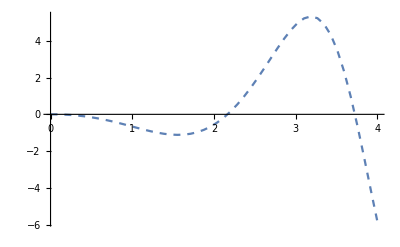

-Graphics-

```mathematica
g1=ListLinePlot[taylorprimer,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g2=ListLinePlot[Heun,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g3=ListLinePlot[Eulermod,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g4=ListLinePlot[RK4,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

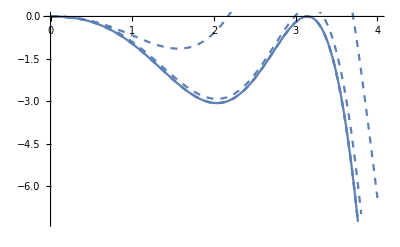

```mathematica
Show[grafanalitica,g1,g2,g3,g4]
```

```mathematica
"AHORA CON 100 PARES"
```

```mathematica
taylorprimer=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Taylorprimer.txt","Table"]
Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Heun.txt","Table"]
Eulermod=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Eulermodificado.txt","Table"]
RK4=Heun=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Rugekutta4.txt","Table"]
```

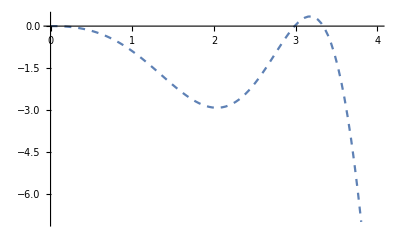

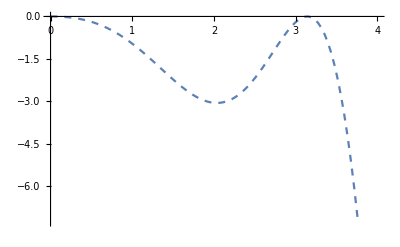

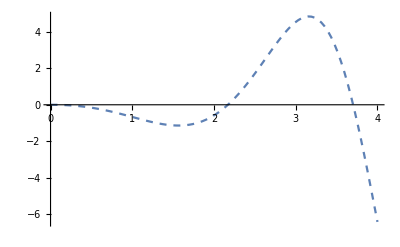

-Graphics-

```mathematica
g1=ListLinePlot[taylorprimer,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g2=ListLinePlot[Heun,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g3=ListLinePlot[Eulermod,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
g4=ListLinePlot[RK4,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

```mathematica
Show[grafanalitica,g1,g2,g3,g4]
```

-Graphics-

```mathematica
"Podemos observar que cuantos más pares de puntos calculamos, más se acercan las figuras a la gráfica de la solución analítica obtenida con mathematica."
```

```mathematica
"EJERCICIO 2"
```

```mathematica
G=DSolve[{q''[t]==-1(((R*C*(q'[t])))+q[t])/(L*C),q[0]==40},q,t][[1,1,2]]
```

Function[{t},40 ⅇ^(1/2 (-200.+(√(-8.+40000. C))/(√C)) t)+ⅇ^(1/2 (-200.-(√(-8.+40000. C))/(√C)) t) C[1]-ⅇ^(1/2 (-200.+(√(-8.+40000. C))/(√C)) t) C[1]]

```mathematica
grafanalitica2=Plot[G[t],{t,0,0.02}]
```

-Graphics-

```mathematica
"No consigo dibujar la solución de la ec diferencial"
```

```mathematica
"Con el programa de Fortran"
```

```mathematica
Iej2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\I(t).txt","Table"]
```

```mathematica
g5=ListLinePlot[Iej2,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

-Graphics-

```mathematica
Qej2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Q(t).txt","Table"]
```

```mathematica
ListLinePlot[Qej2,PlotStyle->Dashing[{Small,Small}],PlotStyle->PointSize[0.03]]
```

-Graphics-

```mathematica
"Con R=0 nos da error el programa"
```

```mathematica
"R=1000"
```

```mathematica
Iej2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\I(t).txt","Table"]
```

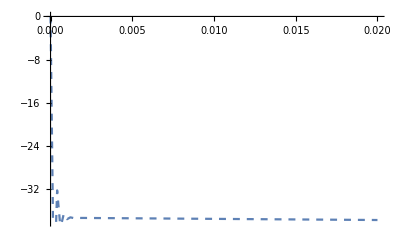

```mathematica
g6=ListLinePlot[Iej2,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

```mathematica
Qej2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Q(t).txt","Table"]
```

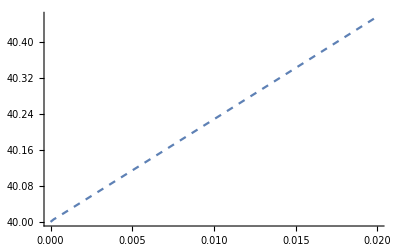

```mathematica
g7=ListLinePlot[Qej2,PlotStyle->Dashing[{Small,Small}],PlotStyle->PointSize[0.03]]
```

```mathematica
"CON R=1500"
```

```mathematica
Iej2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\I(t).txt","Table"]
```

```mathematica
ListLinePlot[Iej2,PlotStyle->Dashed,PlotStyle->PointSize[0.03]]
```

-Graphics-

```mathematica
Qej2=Import["C:\\Users\\Manu\\Desktop\\Programas Fortran\\Métodos numericos 7.12\\Q(t).txt","Table"]
```

```mathematica
ListLinePlot[Qej2,PlotStyle->Dashing[{Small,Small}],PlotStyle->PointSize[0.03]]
```

-Graphics-

```mathematica
El ejercicio 2 hay que repasarlo
```